# TAREA 1: Máximos y mínimos

## Ejemplos

#### Primer Ejemplo

```mathematica
f[x_]:=x^3/3-x^2/2-2x+1/3
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

-2-x+x^2

Busco Puntos Críticos (derivada=0):

{{x→-1},{x→2}}

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico en x=-1:"
f''[-1]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico x=2:"
f''[2]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

-1+2 x

Segunda Derivada en el punto crítico en x=-1:

-3

máximo

Segunda Derivada en el punto crítico x=2:

3

mínimo

Intervalo de Crecimiento (derivada>0):

x<-1||x>2

Intervalo de Decrecimiento (derivada<0):

-1<x<2

Cóncava hacia arriba:

x>1/2

Cóncava hacia abajo:

x<1/2

Gráfico:

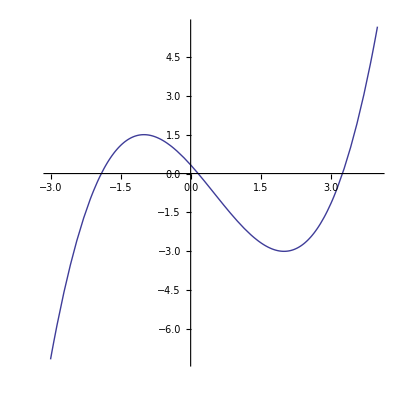

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,-3,4},AspectRatio->1]
```

```mathematica
Clear[f]
```

#### Segundo Ejemplo

```mathematica
f[x_]:=x^4/4-2 x^2+4
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

-4 x+x^3

Busco Puntos Críticos (derivada=0):

{{x→-2},{x→0},{x→2}}

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico en x=-2:"
f''[-2]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico x=0:"
f''[0]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico x=2:"
f''[2]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

-4+3 x^2

Segunda Derivada en el punto crítico en x=-2:

8

mínimo

Segunda Derivada en el punto crítico x=0:

-4

máximo

Segunda Derivada en el punto crítico x=2:

8

mínimo

Intervalo de Crecimiento (derivada>0):

-2<x<0||x>2

Intervalo de Decrecimiento (derivada<0):

x<-2||0<x<2

Cóncava hacia arriba:

x<-2/(√3)||x>2/(√3)

Cóncava hacia abajo:

-2/(√3)<x<2/(√3)

Gráfico:

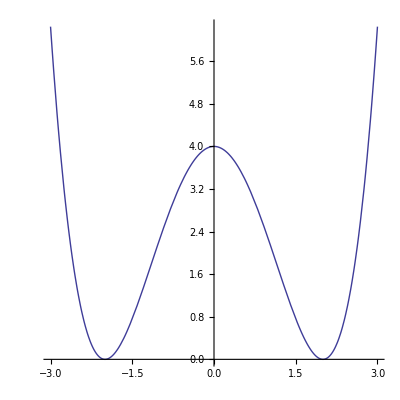

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,-3,3},AspectRatio->1]
```

#### Tercer Ejemplo

```mathematica
f[x_]:=x^3-3x+3
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

-3+3 x^2

Busco Puntos Críticos (derivada=0):

{{x→-1},{x→1}}

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico en x=-1:"
f''[-1]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico x=1:"
f''[1]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

6 x

Segunda Derivada en el punto crítico en x=-1:

-6

máximo

Segunda Derivada en el punto crítico x=1:

6

mínimo

Intervalo de Crecimiento (derivada>0):

x<-1||x>1

Intervalo de Decrecimiento (derivada<0):

-1<x<1

Cóncava hacia arriba:

x>0

Cóncava hacia abajo:

x<0

Gráfico:

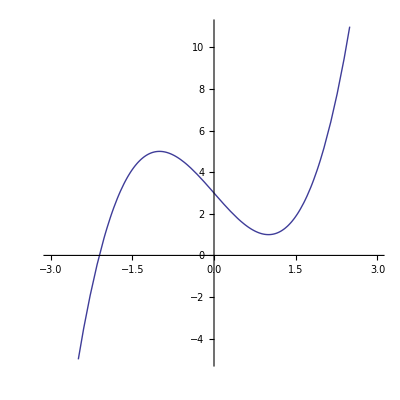

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,-3,3},AspectRatio->1]
```

#### Cuarto Ejemplo

```mathematica
f[x_]:=-2 x^3+6 x^2-3
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

12 x-6 x^2

Busco Puntos Críticos (derivada=0):

{{x→0},{x→2}}

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico en x=0:"
f''[0]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico x=2:"
f''[2]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

12-12 x

Segunda Derivada en el punto crítico en x=0:

12

mínimo

Segunda Derivada en el punto crítico x=2:

-12

máximo

Intervalo de Crecimiento (derivada>0):

0<x<2

Intervalo de Decrecimiento (derivada<0):

x<0||x>2

Cóncava hacia arriba:

x<1

Cóncava hacia abajo:

x>1

Gráfico:

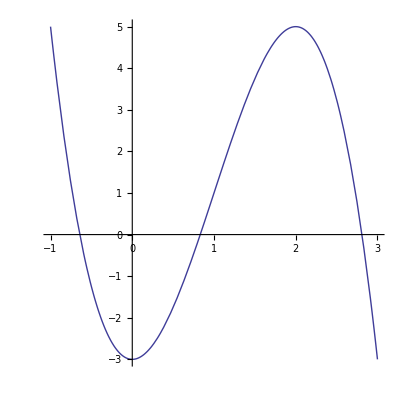

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,-1,3},AspectRatio->1]
```

#### Quinto Ejemplo

```mathematica
f[x_]:=x^2-x^4/8
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

2 x-x^3/2

Busco Puntos Críticos (derivada=0):

{{x→-2},{x→0},{x→2}}

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico en x=-2:"
f''[-2]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico x=0:"
f''[0]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico en x=2:"
f''[2]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

2-(3 x^2)/2

Segunda Derivada en el punto crítico en x=-2:

-4

máximo

Segunda Derivada en el punto crítico x=0:

2

mínimo

Segunda Derivada en el punto crítico en x=2:

-4

máximo

Intervalo de Crecimiento (derivada>0):

x<-2||0<x<2

Intervalo de Decrecimiento (derivada<0):

-2<x<0||x>2

Cóncava hacia arriba:

-2/(√3)<x<2/(√3)

Cóncava hacia abajo:

x<-2/(√3)||x>2/(√3)

Gráfico:

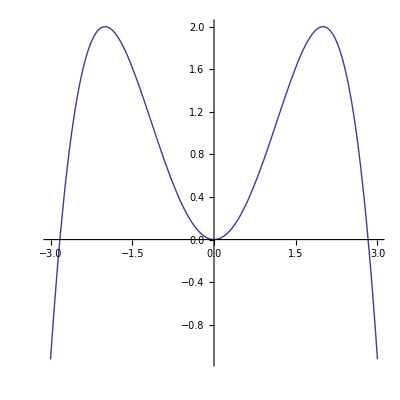

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,-3,3},AspectRatio->1]
```

#### Sexto Ejemplo

```mathematica
f[x_]:=2 x^3+3 x^2-12x-7
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

-12+6 x+6 x^2

Busco Puntos Críticos (derivada=0):

{{x→-2},{x→1}}

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico en x=-2:"
f''[-2]
If[%<0,"máximo","mínimo"]
"Segunda Derivada en el punto crítico x=1:"
f''[1]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

6+12 x

Segunda Derivada en el punto crítico en x=-2:

-18

máximo

Segunda Derivada en el punto crítico x=1:

18

mínimo

Intervalo de Crecimiento (derivada>0):

x<-2||x>1

Intervalo de Decrecimiento (derivada<0):

-2<x<1

Cóncava hacia arriba:

x>-1/2

Cóncava hacia abajo:

x<-1/2

Gráfico:

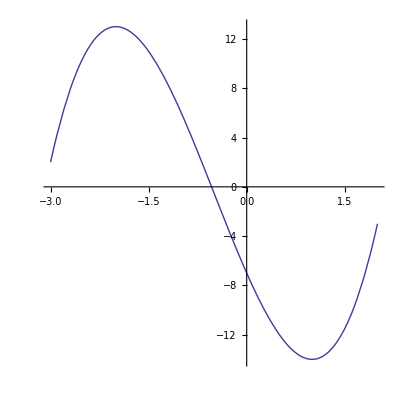

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,-3,2},AspectRatio->1]
```

#### Septimo Ejemplo

```mathematica
f[x_]:=x^2-8Log[x]
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

-8/x+2 x

Busco Puntos Críticos (derivada=0):

{{x→-2},{x→2}}

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico x=2:"
f''[2]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

2+8/x^2

Segunda Derivada en el punto crítico x=2:

4

mínimo

Intervalo de Crecimiento (derivada>0):

-2<x<0||x>2

Intervalo de Decrecimiento (derivada<0):

x<-2||0<x<2

Cóncava hacia arriba:

x<0||x>0

Cóncava hacia abajo:

False

Gráfico:

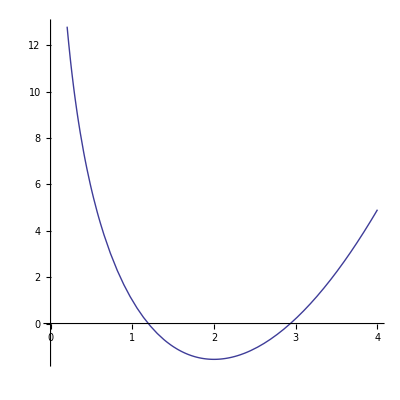

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,0,4},AspectRatio->1]
```

#### Octavo Ejemplo

```mathematica
f[x_]:=1/(√(2π))ⅇ^(-x^2/2)
"Derivada:"
f'[x]
"Busco Puntos Críticos (derivada=0):"
Solve[f'[x]==0,x]
```

Derivada:

-(ⅇ^(-x^2/2) x)/(√(2 π))

Busco Puntos Críticos (derivada=0):

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0}}

```mathematica
N[f[0]]
```

0.398942

```mathematica
"Segunda Derivada"
f''[x]
"Segunda Derivada en el punto crítico en x=0:"
N[f''[0]]
If[%<0,"máximo","mínimo"]
```

Segunda Derivada

-(ⅇ^(-x^2/2))/(√(2 π))+(ⅇ^(-x^2/2) x^2)/(√(2 π))

Segunda Derivada en el punto crítico en x=0:

-0.398942

máximo

Intervalo de Crecimiento (derivada>0):

x<0

Intervalo de Decrecimiento (derivada<0):

x>0

Cóncava hacia arriba:

x<-1||x>1

Cóncava hacia abajo:

-1<x<1

Gráfico:

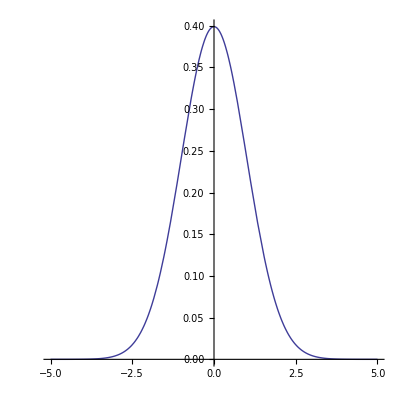

```mathematica
"Intervalo de Crecimiento (derivada>0):"
Reduce[f'[x]>0,x]
"Intervalo de Decrecimiento (derivada<0):"
Reduce[f'[x]<0,x]
"Cóncava hacia arriba:"
Reduce[f''[x]>0,x]
"Cóncava hacia abajo:"
Reduce[f''[x]<0,x]
"Gráfico:"
Plot[f[x],{x,-5,5},AspectRatio->1]
```